```mathematica
qm[matrix_]:=Block[{i, j, k}, Table[Sum[1-KroneckerDelta[matrix[[i]][[j]][[k]]], {k, 1, matrix[[i]][[j]]//Length}], {i, 1, matrix//Length}, {j, 1, matrix[[i]]//Length}]//Transpose]
qv[matrix_]:=Block[{qm=qm[matrix], i, j, k},Table[Sum[1-KroneckerDelta[qm[[i]][[j]]], {j, 1, qm[[1]]//Length}], {i, 1, qm//Length}]]
norm[matrix_]:=Block[{qv=qv[matrix], i, j, k}, Table[Sum[matrix[[i]][[j]][[k]]/qv[[j]], {i, 1, matrix//Length}], {j, 1, matrix[[1]]//Length}, {k, 1, matrix[[1]][[j]]//Length}]]
```

```mathematica
(m1={{1, 0, 0}, {c, 1-c, 0}, {0, 0, 0}})//MatrixForm
(m2={{1, 0, 0}, {0, 0, 0}, {b, 0, 1-b}})//MatrixForm
(m={m1, m2})//MatrixForm

norm[m]//FullSimplifyForPositiveReals//NormalizeRows//Eigenvalues
```

(1 | 0 | 0
c | 1-c | 0
0 | 0 | 0)

(1 | 0 | 0
0 | 0 | 0
b | 0 | 1-b)

((1
0
0) | (c
1-c
0) | (0
0
0)
(1
0
0) | (0
0
0) | (b
0
1-b))

{1,1-b,1-c}

```mathematica
MatrixPower[norm[m]//FullSimplifyForPositiveReals//NormalizeRows, n]//Transpose//Eigenvalues;
entropy=-Total[# Log[#]&/@%]//PowerExpand
entropy/.b->1/10/.c->1-1/1000000000
list=Table[-Total[# Log[#] &/@%], {n, 1, 100}];
ListPlot[list]
```

-(1-b)^n n Log[1-b]-(1-c)^n n Log[1-c]

```mathematica
(a)^n n Log[1/a]/.n->-1/Log[a]
```

-(a^(-1/Log[a]) Log[1/a])/Log[a]

```mathematica
Simplify[-(a^(-1/Log[a]) Log[1/a])/Log[a]]
```

-Log[1/a]/(ⅇ Log[a])

```mathematica
Plot[-Log[1/a]/(ⅇ Log[a]),{a,0,1}]
```

-Graphics-

```mathematica
(a)^n n Log[1/a]
```

```mathematica
D[a^n n Log[1/a], n]
```

a^n Log[1/a]+a^n n Log[1/a] Log[a]

```mathematica
Simplify[a^n Log[1/a]+a^n n Log[1/a] Log[a]]
```

```mathematica
a^n Log[1/a] (1+n Log[a])==0
```

a^n Log[1/a] (1+n Log[a])==0

```mathematica
Solve[a^n Log[1/a] (1+n Log[a])==0&&n∈Integers,{n}]
```

{{n→ConditionalExpression[-1/Log[a], 1/Log[a]∈ℤ]}}

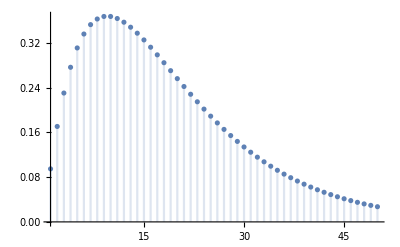

```mathematica
DiscretePlot[(9/10)^n n Log[10/9],{n,1,50}]
```

```mathematica
entropy/.n->-1/Log[1-b]/.c->1/2 b
```

(1-b)^(-1/Log[1-b])+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]

```mathematica
Simplify[(1-b)^(-1/Log[1-b])+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]]
```

```mathematica
1/ⅇ+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]//ExpToTrig
```

Cosh[1]+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]-Sinh[1]

```mathematica
Simplify[Cosh[1]+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]-Sinh[1]]
```

```mathematica
1/ⅇ+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]//FullSimplifyForPositiveReals
```

1/ⅇ+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]

```mathematica
Together[1/ⅇ+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]]
```

((1-b/2)^(-1/Log[1-b]) ((1-b/2)^(1/Log[1-b]) Log[1-b]+ⅇ Log[1-b/2]))/(ⅇ Log[1-b])

```mathematica
FullSimplify[((1-b/2)^(-1/Log[1-b]) ((1-b/2)^(1/Log[1-b]) Log[1-b]+ⅇ Log[1-b/2]))/(ⅇ Log[1-b])]
```

1/ⅇ+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b]

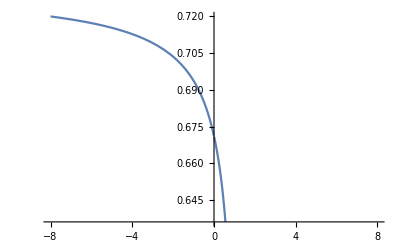

```mathematica
Plot[((1-b/2)^(-1/Log[1-b]) ((1-b/2)^(1/Log[1-b]) Log[1-b]+ⅇ Log[1-b/2]))/(ⅇ Log[1-b]),{b,-8,8}]
```

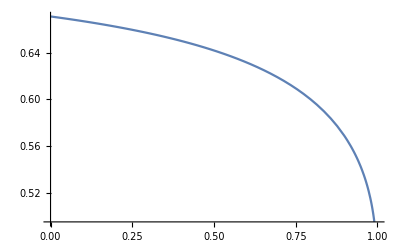

```mathematica
Plot[1/ⅇ+((1-b/2)^(-1/Log[1-b]) Log[1-b/2])/Log[1-b],{b,0,1}]
```

```mathematica
Simplify[2 (1-b)^(-1/Log[1-b])]
```

2/ⅇ

```mathematica
N[2/ⅇ]
```

0.735759

```mathematica
FullSimplify[-(1-b)^n Log[1-b]-(1-b)^n n Log[1-b]^2-(1-c)^n Log[1-c]-(1-c)^n n Log[1-c]^2]
```

```mathematica
-(1-b)^n Log[1-b] (1+n Log[1-b])-(1-c)^n Log[1-c] (1+n Log[1-c])/.c->b
```

```mathematica
-2 (1-b)^n Log[1-b] (1+n Log[1-b])==0
```

-2 (1-b)^n Log[1-b] (1+n Log[1-b])==0

```mathematica
Solve[-2 (1-b)^n Log[1-b] (1+n Log[1-b])==0,{n}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→-1/Log[1-b]}}

```mathematica
FindInstance[-(1-b)^n Log[1-b]-(1-b)^n n Log[1-b]^2-(1-c)^n Log[1-c]-(1-c)^n n Log[1-c]^2==0,{b,c,n}]
```

{{b→0,c→0,n→0}}

```mathematica
FullSimplify[-(1-b)^n Log[1-b]-(1-b)^n n Log[1-b]^2-(1-c)^n Log[1-c]-(1-c)^n n Log[1-c]^2]
```

-(1-b)^n Log[1-b] (1+n Log[1-b])-(1-c)^n Log[1-c] (1+n Log[1-c])

```mathematica
-Log[1/a]/(ⅇ Log[a])//FullSimplifyForPositiveReals
```

1/ⅇ

```mathematica
N[1/ⅇ]
```

0.367879